```mathematica
ClearAll["Global`*"];
```

```mathematica
txtF[txt_]:=Item[Style[txt,"Panel",20,Background->Pink,RGBColor[0.32,0.42,0.65]],Background->Pink,Frame->True]
Manipulate[Column[{Plot[wave[x,f],{x,-50,50},ColorFunction->"Rainbow",ImageSize->Medium],Switch[text,1,txtF[" Long Radio Wave\nThis is the Long Radio Wave\n It's wave length is between 10^2 to 10^8 meters"],2,txtF[" Short Radio Wave\n This is the Short Radio Wave\n It's wave length is between 1 to 10^2 meters"],3,txtF[" Microwave\n This is the Microwave\n It's wave length is between 10^-3 to 1 meters"],4,txtF[" IR\n This the IR wave\n It's wave length is between 10^-6 to 10^-3 meters."],5,txtF[" Visible Spectrum\n These are waves that is visible to human eyes.\n It's wave length is between 10^-7 to 10^-6 meters"],6,txtF[" UV\n This is the UV wave\n It's wave length is around 10^-7 meters"],7,txtF[" EUV\n This is EUV wave.\n It's wave length is around 10^-8 meters"],8,txtF[" SX\n This is Soft X-ray\n It's wave length is around 10^-9 meters"],9,txtF[" HX\n This is Hard X-ray\n It's wave length is around 10^-10 meters"],10,txtF[" γ\n This is γ wave\n It's wave length is around 10^-12 meters"]]},Center],{{f,1,"frequency"},1,10,1,ControlType->Slider},{{text,1,"content"},1,10,1,ControlType->Slider},Initialization:>(wave[x_,f_]:=Cos[f*x]+Sin[f*x])]
```

```mathematica
Manipulate[Module[{text,waveFunc,text2,lightspeed},text ={Style[" Long Radio Wave\n This is the Long Radio Wave\n It's wave length is between 10^2 to 10^8 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],Style[" Short Radio Wave\n This is the Short Radio Wave\n It's wave length is between 1 to 10^2 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],Style[" Microwave\n This is the Microwave\n It's wave length is between 10^-3 to 1 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],Style[" IR\n This the IR wave\n It's wave length is between 10^-6 to 10^-3 meters.",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],Style[" Visible Spectrum\n These are waves that is visible to human eyes.\n It's wave length is between 10^-7 to 10^-6 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],Style[" UV\n This is the UV wave\n It's wave length is around 10^-7 mters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],Style[" EUV\n This is EUV wave.\ It's wave length is around 10^-8 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],Style[" SX\n This is Soft X-ray\n It's wave length is around 10^-9 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],Style[" HX\n This is Hard X-ray\n It's wave length is around 10^-10 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],Style[" γ\n This is γ wave\n It's wave length is around 10^-12 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20]};
waveFunc[x_,f_]:= Cos[f*x]+Sin[f*x];
text2[f_]:= Style[ToString[Round[lightspeed/f]]];
lightspeed = 3*10^8;
Row[{Grid[{{Show[Plot[waveFunc[x,f],{x,-6,6},ColorFunction->"Rainbow",Axes-> False,ImageSize->Medium]]},{Text[Style[Column[{"Frequency: ",ToString[NumberForm[f,{5,3}]]<>" Hz","","Wavelength: ",ToString[NumberForm[lightspeed/f,{5,3}]]<>" m"},Alignment->Right]]]}}],Grid[{{text[[Floor[f]]]}},Frame->True,Background->LightPink]}]], {{f,1,"frequency"},1,10,0.1,ControlType-> Slider},
TrackedSymbols:>True,
SynchronousInitialization->False,
AutorunSequencing->{2,3},
ContentSize->{700, 560}]
```

```mathematica
DynamicModule[{x={0,0,0}},EventHandler[{Annotation[Graphics[{Red,Disk[]},PlotLabel->Dynamic[x[[1]]]],1,"Mouse"],Annotation[Graphics[{Green,Disk[]},PlotLabel->Dynamic[x[[2]]]],2,"Mouse"],Annotation[Graphics[{Blue,Disk[]},PlotLabel->Dynamic[x[[3]]]],3,"Mouse"]},{"MouseClicked":>(x[[MouseAnnotation[]]]=x[[MouseAnnotation[]]]+1)}]]
```

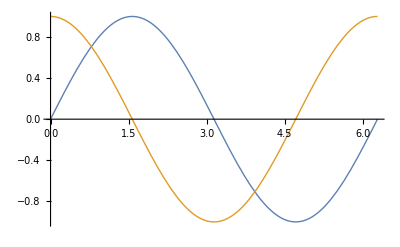

```mathematica
Plot[{Annotation[Sin[x],"Sine","Mouse"],Annotation[Cos[x],"Cosine","Mouse"]},{x,0,2 π},PlotStyle->Thick]
```

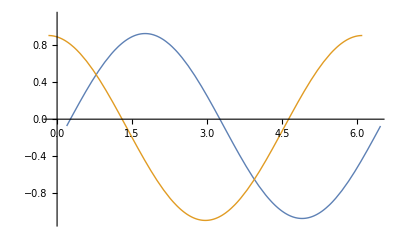

-Graphics-

```mathematica
DynamicModule[{lectureText = {Grid[{{Style["Text 1",Blue,FontFamily->"Arial",FontSize-> 24]}},Frame->True],Grid[{{Style["Text 2",Blue,FontFamily->"Arial",FontSize-> 24]}},Frame->True],Grid[{{Style["Text 3",Blue,FontFamily->"Arial",FontSize-> 24]}},Frame->True],Grid[{{Style["Text 4",Blue,FontFamily->"Arial",FontSize-> 24]}},Frame->True],Grid[{{Style["Text 5",Blue,FontFamily->"Arial",FontSize-> 24]}},Frame->True],Grid[{{Style["Text 6",Blue,FontFamily->"Arial",FontSize-> 24]}},Frame->True],Grid[{{Style["Text 7",Blue,FontFamily->"Arial",FontSize-> 24]}},Frame->True],Grid[{{Style["Text 8",Blue,FontFamily->"Arial",FontSize-> 24]}},Frame->True],Grid[{{Style["Text 9",Blue,FontFamily->"Arial",FontSize-> 24]}},Frame->True],Grid[{{Style["Text 10",Blue,FontFamily->"Arial",FontSize-> 24]}},Frame->True]}},EventHandler[{Annotation[Graphics[{Red,Disk[]},PlotLabel->Dynamic[lectureText[[1]]]],1,"Mouse"],Annotation[Graphics[{Green,Disk[]},PlotLabel->Dynamic[lectureText[[2]]]],2,"Mouse"],Annotation[Graphics[{Blue,Disk[]},PlotLabel->Dynamic[lectureText[[3]]]],3,"Mouse"]},{"MouseClicked":>(Grid[{{Style[lectureText[[i]]]}}])}]]
```

```mathematica
DynamicModule[{x={0,0,0}},EventHandler[Annotation[Graphics3D[{Red,Sphere[]},PlotLabel->Dynamic[x[[1]]]],1,"Mouse"],Annotation[Graphics3D[{Green,Sphere[]},PlotLabel->Dynamic[x[[2]]]],2,"Mouse"],Annotation[Graphics3D[{Blue,Sphere[]},PlotLabel->Dynamic[x[[3]]]],3,"Mouse"],{"MouseClicked":>(x[[MouseAnnotation[]]]=x[[MouseAnnotation[]]]+1)}]]
```

```mathematica
DynamicModule[{lectureText={"Text 1","Text 2","Text 3","Text 4","Text 5","Text 6","Text 7","Text 8","Text 9","Text 10"}},EventHandler[{Annotation[Graphics3D[{Red,Sphere[]},PlotLabel->Dynamic[lectureText[[1]]]],1,"Mouse"],Annotation[Graphics3D[{Green,Sphere[]},PlotLabel->Dynamic[lectureText[[2]]]],2,"Mouse"],Annotation[Graphics3D[{Blue,Sphere[]},PlotLabel->Dynamic[lectureText[[3]]]],3,"Mouse"]},{"MouseClicked":>(Print[Grid[{{Style[lectureText[[MouseAnnotation[]]],Blue,FontFamily->"Arial",FontSize-> 24]}},Frame-> True]])}]]
```